# Deep Learning for Text Analysis

## Natural Language Net Toolbox

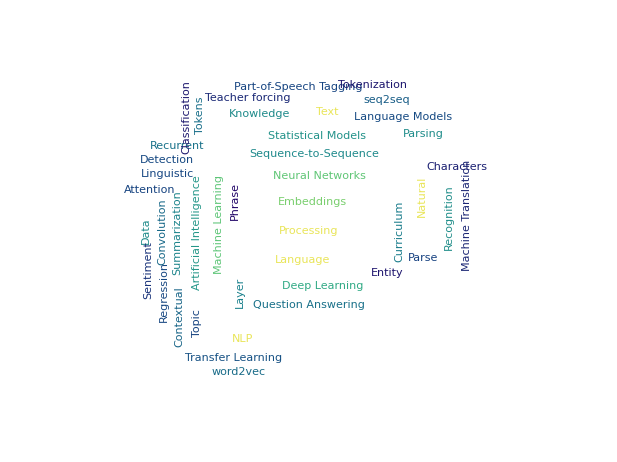

## Neural Net Toolbox for Natural Language

### Natural Language Tasks

“Sequence to something”, typical natural language processing tasks

### (In/Out)put (Pre-/Post-)processing

Net(De/En)coder

Byte pair encoding (BPE)

### Learnable Element Representation

WordEmbedding

### Sequence-to-Sequence Operations:

ThreadingLayer, NetMapOperator, NetThreadingOperator

Convolution (CNN): ConvolutionLayer

Recurrent neural net (RNN): BasicRecurrentLayer, GatedRecurrentLayer, LongShortTermMemoryLayer, NetFoldOperator

Transformers net: AttentionLayer

### Sequence-to-Vector Operations

SequenceLastLayer, PoolingLayer

### A Sequence-to-Sequence Toy Model

## Natural Language Tasks: “Sequence to Something”

### Sequence

Length unknown prior to training/evaluation.

Order maters, context can change meaning of elements  far apart from each others.

### Common Tasks

Text classification (word sequence [Text] → class label):

sentiment analysis, topic classification, language detection

My phone broke again → Negative
I love eating carrots in the morning → FoodAndDrink
la maison est bleue → French

Tagging/annotating (word sequence [Text] → sequence of classes labels):

part-of-speech (POS) tagging

NYC | ,  | Los Angeles | , and  | Chicago |  are the largest cities in the  | USA |  in  | 2018 | .
City |  | City |  | City |  | Country |  | Date |

Text parsing:

building grammar tree

The
Determinercat
Noun
Noun Phrase  sat
Verb  on
Preposition  the
Determinermat
Noun
Noun Phrase
Prepositional Phrase
Verb Phrase.
Punctuation
Sentence

Text generation (word sequence):

language modeling, question answering, optical characters/speech recognition

The car sat on the  → mat
{Brian was in the bedroom. Brian moved to the kitchen, Where is Brian?} → kitchen
-Graphics-→ Dear Mind, please stop thinking so much at night, I need to sleep.

## (In/Out)put (Pre-/Post-)processing

### NetEncoder/NetDecoder

Net input preprocessing from text to sequence: tokenization:

character-wise

```mathematica
netencoder = NetEncoder["Characters"]
```

```mathematica
netencoder["The cat sat on the mat."]
```

Out-of-vocabulary issue:

```mathematica
netencoder["Greek is δροσερός"]
```

```mathematica
dictionnary = netencoder[["Alphabet"]]
```

```mathematica
NetEncoder[{"Characters", Append[dictionnary, _]}]["Greek is δροσερός"]
```

byte level

```mathematica
NetEncoder["UTF8"]["Greek is δροσερός"]
```

word level

```mathematica
NetEncoder["Tokens"]["The cat sat on the mat"]
```

sub-word level: pretrained byte pair encoding

```mathematica
netencoderBPE=NetExtract[NetModel["BPEmb Subword Embeddings Trained on Wikipedia Data"], "Input"]
```

```mathematica
index = netencoderBPE["The cat sat on the catmat. Greek is δροσερός"]
```

{8,1594,1802,72,8,1594,4170,49936,2725,81,49913,1}

```mathematica
NetExtract[netencoderBPE,"Tokens"][[index]]
```

{ the, cat, sat, on, the, cat,mat,., greek, is, ,_}

## Learnable Element Representation

### Embeddings

Each token is attached to a learned vector in a lookup table

```mathematica
embbeding = EmbeddingLayer[5, 3]
```

Values are randomly initialized

```mathematica
embbeding =NetInitialize@embbeding
```

```mathematica
MatrixPlot[#, FrameTicks->{All, None}]&@embbeding[{1,2,1}]
```

As learning progresses, vector values become meaningful—see with a pretrained one available from the Wolfram Net Repository™

See: GloVe: Global Vectors for Word Representation, J. Pennington, R. Socher and C. D. Manning (2014)

```mathematica
glove=NetModel["GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

```mathematica
animals={"Alligator","Bear","Bird","Bee","Camel","Zebra","Crocodile","Rhinoceros","Giraffe","Dolphin","Duck","Eagle","Elephant","Fish","Fly"};
colors={"Blue","White","Yellow","Purple","Red","Black","Green","Grey"};
fruits={"Apple","Apricot","Avocado","Banana","Blackberry","Cherry","Coconut","Cranberry","Grape","Mango","Melon","Papaya","Peach","Pineapple","Raspberry","Strawberry","Fig"};
```

```mathematica
label[str_]:= Labeled[str,Style["⊙", Which[MemberQ[animals, str], Blue,MemberQ[fruits, str],  Green, True, Red]]]
```

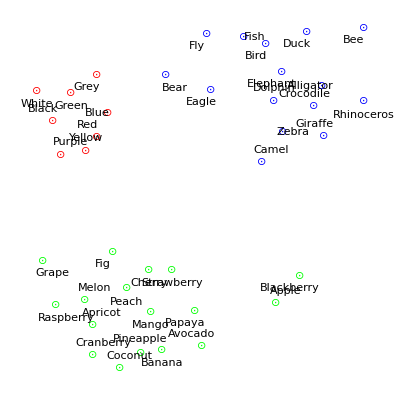

```mathematica
FeatureSpacePlot[label/@Join[animals, fruits, colors],FeatureExtractor->glove]
```

More elaborated models generate context-dependent values (seen later)

## Sequence-to-Sequence

### Sequence Processing Patterns

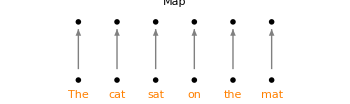
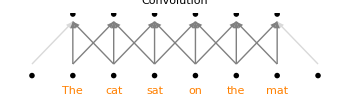
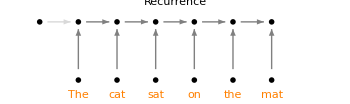
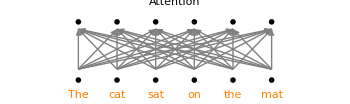

## Sequence-to-Sequence

### ThreadingLayer

Thread a function over a sequence

```mathematica
seq = Table[RandomReal[1.,{l, 5}], {l, {5, 3,4}}];
```

```mathematica
VectorSequencesPlot[seq]
VectorSequencesPlot[ThreadingLayer[Sin[#+1]&][seq]]
```

### NetMapOperator

Thread a network over a sequence

```mathematica
innerNet = LinearLayer[4, "Input" -> {5}]
```

```mathematica
innerNet = NetInitialize[innerNet]
```

```mathematica
VectorSequencesPlot@seq[[1, 1]]
VectorSequencesPlot@innerNet[seq[[1, 1]]]
```

```mathematica
seqNet = NetMapOperator[innerNet]
```

```mathematica
VectorSequencesPlot@seq
VectorSequencesPlot@seqNet[seq]
Map[innerNet, seq] ≃ seqNet[seq] (* rounding precision ≃ corresponds to "at 10^*-6 equal" *)
```

Notice the differences despite sometimes similar evaluation results

```mathematica
TableForm[Outer[Check[VectorSequencesPlot[#1[#2]],$Failed]&, {innerNet, NetMapOperator[innerNet], Map[innerNet]},{seq[[1,1]], seq[[1]], seq},1], TableHeadings->{{"LinearLayer","NetMapOperator[LinearLayer]","Map[LinearLayer]"},{"Vector","Vector batch / Sequence", "Sequence batch"}}, TableAlignments->Center]
```

### CatenateLayer, NetMapThreadOperator

Takes several

No connectivity—no added context

## Sequence-to-Sequence

### Convolution Net (CNN): ConvolutionLayer

See: Deep Speech 2: End-to-End Speech Recognition in English and Mandarin by D. Amodei et al. available from the Wolfram Net Repository™ as Deep Speech 2 Trained on Baidu English Data

Propagating information from the local neighborhood:

beware of the dimension where convolution is applied, i.e. channel position—default corresponds to 2D image case

```mathematica
NetInitialize[ConvolutionLayer[5, 3, "Input"-> {"Varying", 5}]]
```

sequence-wise convolution requires “Interleaving”→True

```mathematica
convnet = ConvolutionLayer[1, 3, "Interleaving"->True,"Input"-> {"Varying", 2}]
```

```mathematica
Manipulate[
	Graphics[Catenate[Table[
		Block[{h=2,r=0.15, nouts, shift, layer0Pts, layer1Pts, inputs, outputs},
			nouts = Max[1,(9-KernelSize)/Stride+1];
			shift = (KernelSize-1)/2;
			layer0Pts = Thread[{Range[1,9],0}];
			layer1Pts = Thread[{(Stride*Range[0,nouts-1]+shift+1),h}];
			inputs = Take[allinputs, Length[layer0Pts]];
			outputs = Take[alloutputs, Length[layer1Pts]];
			{
				{Gray,Arrowheads[Small],With[{pt=layer1Pts⟦k⟧},Map[Function[pt1,Arrow[{MapAt[(#+0.2)&,pt1,2],MapAt[(#-0.2)&,pt,2]}]],Partition[layer0Pts,KernelSize,Stride]⟦k⟧]]},
				{MapThread[Inset[#1,#2]&,{inputs, layer0Pts}]},
				{MapThread[Inset[#1,#2]&,{outputs, layer1Pts}]}
			}
		],
		{k, Range[Max[1,(9-KernelSize)/Stride+1]]}
	]]],
	{{KernelSize, 3}, 1, 9, 2},
	{{Stride, 1}, 1, 3, 1},
	Delimiter,Dynamic[With[{ks=KernelSize, s=Stride},
		Style[With[{args = {Style[Placeholder[],Gray],Style[{ks},Orange],Style["Stride"->s,Orange],Style["Interleaving"->True,Gray],Style["Input"->{"n",Placeholder[]},Gray]}},
			Apply[HoldForm@*ConvolutionLayer,args]],
			Black,ShowStringCharacters -> True]
		
	]],
	ControlType -> {PopupMenu,PopupMenu},
	Initialization :> (
		SeedRandom[1970];
		allinputs = Table[Rasterize[ArrayPlot[RandomReal[1,{3,1}],FrameTicks->None,Frame->False], ImageSize->7,Background->White], 9];
		alloutputs = Table[Rasterize[ArrayPlot[RandomReal[1,{3,1}],FrameTicks->None,Frame->False], ImageSize->7,Background->White], 9];
	)
]
```

```mathematica
weights = {{{-1, 2, -1}, {0,0,0}}};
convnet = NetReplacePart[convnet, {"Weights"->weights, "Biases" -> None}]
```

```mathematica
seq = {RandomReal[1.,{9, 2} ],RandomReal[1., {11, 2}]};
```

```mathematica
VectorSequencesPlot[seq]
VectorSequencesPlot[convnet[seq]]
```

```mathematica
NetModel["Deep Speech 2 Trained on Baidu English Data", "UninitializedEvaluationNet"]
```

Causal convolution uses only past information, equivalent to a shift in sequences of corresponding elements; achieved in Mathematica^® using padding

See: WAVENET: a Generative Model for raw Audio by A. van den Oord, S. Dieleman et al.

```mathematica
casualCNN = NetInitialize@NetChain[
	Table[
		ConvolutionLayer[
			1,
			{2},
			"Dilation"->2^i,
			"PaddingSize"->{{2^i,0}},
			"Interleaving"->True
			],
		{i, Range[0, 3]}
		],
		"Input"->{"Varying", 1}
		]
```

Low memory footprint

Helps to encode lengthy sequences into shorter ones for further processing

Low footprint features extractor/sub-sampler

## Sequence-to-Sequence

### Recurrent Neural Net (RNN): RecurrentLayer, NetFoldOperator

Similar to FoldList function, recurrent layers reuse their state vector from previous computation step

BasicRecurrentLayer:

combines current values to the previous result

s_t=Tanhpaclet:ref/Tanh[w_i.x_t+w_s.s_(t-1)+b]

```mathematica
basicRec = BasicRecurrentLayer[4, "Input"-> {"Varying",5}]
```

```mathematica
basicRec= NetInitialize[basicRec]
```

```mathematica
basicInner = BRinner[4, "Input"-> 5];
positions = Keys@Information[basicInner, "Arrays"];
arrays = Values@Information[basicRec, "Arrays"];
basicInner =NetReplacePart[basicInner, Thread[positions -> arrays]]
```

```mathematica
handWrittenBasicRec = NetFoldOperator[basicInner]
```

```mathematica
seq = Table[RandomReal[1., {l, 5}], {l, {5, 3, 7, 23}}];
VectorSequencesPlot[seq]
```

```mathematica
VectorSequencesPlot[basicRec@seq]
basicRec@seq ≃ handWrittenBasicRec@seq
```

Fast, not (very) powerful

Memory usage growing with sequence length (especially at training)

### All Recurrent Layers Tips

NetPort[“State”] can be exposed through NetGraph to provide the initial value

```mathematica
basicRecState=NetGraph[{basicRec}, {NetPort["State"]-> NetPort[1, "State"]}]
VectorSequencesPlot@basicRecState[<|"Input"-> seq, "State"-> RandomReal[.1, {Length@seq,4}]|>]
```

Warning: dropout regularization (detailed later) affecting sequence-wise flow of information can be catastrophic for learning:

See: A Theoretically Grounded Application of Dropout in Recurrent Neural Networks by Y. Gal, and Z. Ghahramani (2015)

```mathematica
Options[BasicRecurrentLayer]
```

inside recurrent layers family use "VariationnalXXX" dropout method (same mask along a sequence); use “StateUpdate” at your own risk

```mathematica
BasicRecurrentLayer[4, "Input"-> {"Varying",5}, "Dropout"-> .1]
```

## Sequence-to-Sequence

### Recurrent Neural Net (RNN): LongShortTermMemoryLayer (LSTM)

See: Long Short-Term Memory by S. Hochreiter and J. Schmidhuber (1999)

Improve basic recurrent layer on learning long-range correlations: memorize/forget:

analog gates control signal flow

cell can maintain its value for a long time when “forget” gate is strong and “input” weak

input and state generate a new memory candidate

input and state control the gates:

forget: drops cell content

input: adds memory content to cell

output: weights new state

i_t=LogisticSigmoidpaclet:ref/LogisticSigmoid[W_ix.x_t+W_is.s_(t-1)+b_i]
o_t=LogisticSigmoidpaclet:ref/LogisticSigmoid[W_ox.x_t+W_os.s_(t-1)+b_o]
f_t=LogisticSigmoidpaclet:ref/LogisticSigmoid[W_fx.x_t+W_fs.s_(t-1)+b_f]
m_t=Tanhpaclet:ref/Tanh[W_mx.x_t+W_ms.s_(t-1)+b_m]
c_t=f_t*c_(t-1)+i_t*m_t
s_t=o_t*Tanhpaclet:ref/Tanh[c_t]

```mathematica
lstm = NetInitialize@LongShortTermMemoryLayer[4, "Input"-> {"Varying", 5}]
```

```mathematica
innerLSTM = LSTMinner[4, "Input"-> 5];
names = Keys@Information[innerLSTM, "Arrays"];
arrays = Values@Information[lstm, "Arrays"];
innerLSTM = NetReplacePart[innerLSTM,Thread[names -> arrays]]
```

```mathematica
handWrittenLSTM = NetFoldOperator[innerLSTM,{"Output"-> "State", "Cell"-> "PrevCell"}]
```

```mathematica
seq = Table[RandomReal[1.,{l, 5}], {l, {7,4, 5}}];
VectorSequencesPlot[seq]
VectorSequencesPlot[lstm[seq]]
lstm[seq]≃handWrittenLSTM[seq, "Output"]
```

State of the art before attention; slow to train, non-monotonic training curves

Hardly finds out correlations between elements far apart

Larger memory usage

## Sequence-to-Sequence

### Recurrent Neural Net (RNN): GatedRecurrentLayer (GRU)

See: On the properties of neural machine translation: Encoder-decoder approaches, K. Cho, Y. Bengio et al. (2014)

Similar in spirit, yet simpler than the LSTM, GRU still exhibits good performances and is much faster to compute:

state and memory cell regrouped

“input” is “(1-forget)” now called “reset”, all in one gate

```mathematica
Subscript[i, t]=LogisticSigmoidpaclet:ref/LogisticSigmoid[Subscript[W, ix].Subscript[x, t]+Subscript[W, is].Subscript[s, t-1]+Subscript[b, i]]
Subscript[r, t]=LogisticSigmoidpaclet:ref/LogisticSigmoid[Subscript[W, rx].Subscript[x, t]+Subscript[W, rs].Subscript[s, t-1]+Subscript[b, r]]
Subscript[m, t]=Tanhpaclet:ref/Tanh[Subscript[W, mx].Subscript[x, t]+Subscript[r, t]*(Subscript[W, ms].Subscript[s, t-1])+Subscript[b, m]]
Subscript[s, t]=(1-Subscript[i, t])*Subscript[m, t]+Subscript[i, t]*Subscript[s, t-1]
```

```mathematica
gru = NetInitialize@GatedRecurrentLayer[4, "Input"-> {"Varying", 5}]
```

```mathematica
gruInner = GRUinner[4,"Input"-> 5];
arrays = Values@Information[gru, "Arrays"];
names = Keys@Information[gruInner, "Arrays"];
gruInner =NetReplacePart[gruInner,Thread[names -> arrays]]
```

```mathematica
handWrittenGRU = NetFoldOperator[gruInner,{"Output"-> "State"}]
```

```mathematica
seq = Table[RandomReal[1., {l, 5}], {l, {4,7,3}}];
```

```mathematica
VectorSequencesPlot@seq
VectorSequencesPlot@gru[seq]
gru[seq]≃handWrittenGRU[seq]
```

Quite a bit faster than LSTM, similar performances in many cases

Less memory than LSTM

## Sequence-to-Sequence

### Recurrent Neural Net (RNN): NetBidirectionalOperator

How to propagate information from the future as well?

```mathematica
bigru = NetBidirectionalOperator[NetInitialize@GatedRecurrentLayer[4,"Input" -> {"Varying",5}]]
```

```mathematica
gruInner = GRUinner[4,"Input"-> 5];
names = Keys@Information[gruInner, "Arrays"];
arrays = Values@Information[bigru[["ForwardNet"]], "Arrays"];
gruInner =NetReplacePart[gruInner,Thread[names -> arrays]];
homeforwardgru = NetFoldOperator[gruInner,{"Output"-> "State"}];
homebigru = BidirectionnalOp[homeforwardgru]
```

```mathematica
seq = Table[RandomReal[1., {l, 5}], {l, {5,5,4}}];
```

```mathematica
VectorSequencesPlot@seq
VectorSequencesPlot@bigru[seq]
bigru[seq] ≃ homebigru[seq]
```

The sequence-to-sequence state of the art before attention

Cannot be used for generative model (seeing the future helps “too much”)

In general, do not build blocks or model from scratch

## Sequence-to-Sequence

### Transformers Net: AttentionLayer

See: Attention Is All You Need, A. Vaswani, I. Polosukhin et al., (2017)

```mathematica
-Graphics--Graphics-
```

from: Neural Machine Translation by Jointly Learning to Align and Translate, D. Bahdanau, Y. Bengio et al. (2014)

Weight the contribution of each element over whole sequence span—like a human “focus”

Self-attention: is a special case when “Query” is identical to “Keys/Values”

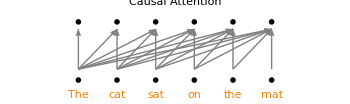
```mathematica
-Graphics--Graphics-{{-Graphics-}, {-Graphics-}}
```

```mathematica
attention = NetInitialize@AttentionLayer[
"Key"-> {"Varying", 5},
"Value"-> {"Varying", 5},
"Query"->{"Varying", 5} ]
```

```mathematica
seq = Table[RandomReal[1., {l, 5}], {l, {5,6,4}}];
VectorSequencesPlot@seq
VectorSequencesPlot@attention[<|"Key" -> seq, "Value" -> seq, "Query" -> seq|>]
```

```mathematica
multiattention = NetInitialize@AttentionLayer[
 "Key"-> {"Varying", 5,3},
"Value"-> {"Varying", 5, 3},
"Query"->{"Varying", 5,3},
"MultiHead"-> True,
"Mask"-> "Causal"]
```

Computationally intensive (square of sequence length)

Unaware of values ordering !!

use positional encoding

```mathematica
NetExtract[NetModel["GPT-2 Transformer Trained on WebText Data", "UninitializedEvaluationNet"], "embedding"]
```

See: Language Models are Unsupervised Multitask Learners, A. Radford, I. Sutskever et al. (2019)

## Sequence-to-Vector Operations

### SequenceLastLayer

The obvious one… but has information propagated there?

```mathematica
VectorSequencesPlot[seq]
Row@Map[VectorSequencesPlot]@SequenceLastLayer[][seq]
```

### Aggregation, Pooling

Merge sequence-wise with a pooling function among Min, Max, Mean locally (like a convolution) or globally

```mathematica
VectorSequencesPlot[seq]
VectorSequencesPlot[PoolingLayer[3,"Interleaving"->True,"Input"->{"Varying",Automatic}][seq]]
Row@Map[VectorSequencesPlot]@AggregationLayer[Max,1,"Input"->{"Varying",Automatic}][seq]
```

## A Sequence-to-Sequence Toy Model

### Integer Additions on Strings

See the tutorial.

```mathematica
-Graphics--Graphics-
```

```mathematica
{testdata, traindata} = MakeIntegerData[];
traindata[[;;3]]
```

```mathematica
inputEnc=NetEncoder[{"Characters",{DigitCharacter,"+"}}]
inputEnc[traindata[[1,1]]]
```

With unknown target length, end and beginning of target sequence are indicated with a specific token at training (to initialize generation and know when to stop)

```mathematica
targetEnc=NetEncoder[{"Characters",{DigitCharacter,{StartOfString,EndOfString}->Automatic}}]
targetEnc[traindata[[1,2]]]
```

Recurrent processing to encode the sequence

```mathematica
encoderNet=NetGraph@NetChain[{EmbeddingLayer[16],GatedRecurrentLayer[128],SequenceLastLayer[]}]
```

Recurrent decoding of the encoded input

```mathematica
decoderNet=NetGraph[{
EmbeddingLayer[16],
GatedRecurrentLayer[128],
NetMapOperator[LinearLayer[]],
SoftmaxLayer[]},
{NetPort["Previous"]->1->2->3->4,
NetPort["Encoding"]->NetPort[2,"State"]}
]
```

Sequence-to-sequence net

```mathematica
net=NetGraph[<|"encoder"->encoderNet,"decoder"->decoderNet|>,
{NetPort["Input"]->"encoder"->NetPort["decoder","Encoding"]}]
```

Attach loss for teacher-forcing training:

expected (known) target element is fed back to the net during training

this is equivalent to shifting target sequence by one element {11,9,1,10,11}

```mathematica
(*SequenceMost*){11,9,1,10} -> {9,1,10,11} (*SequenceRest*)
```

```mathematica
trainingNet=NetGraph[<|"student"-> net,"loss"->CrossEntropyLossLayer["Index"],"rest"->SequenceRestLayer[], "most"-> SequenceMostLayer[]|>,
{NetPort["Input"]->NetPort["student", "Input"],
NetPort["Target"]->"most" ->NetPort["student","Previous"],
NetPort["student","Output"]->NetPort["loss","Input"],
NetPort["Target"]->"rest"->NetPort["loss","Target"]},
"Input"->inputEnc,"Target"->targetEnc]
```

Train the net

```mathematica
result=NetTrain[trainingNet,trainingData,All,ValidationSet->testData,MaxTrainingRounds->50];
trainedNet=result["TrainedNet"]
```

To generate, encoding is first computed and decoder is fed its previous guess to complete it one element at a time until end token is met

```mathematica
encoder = NetReplacePart[NetExtract[trainedNet, {"student","encoder"}], "Input"-> NetExtract[trainedNet, "Input"]]
decoder = NetReplacePart[NetExtract[trainedNet, {"student","decoder"}],
{"Previous" -> NetEncoder[{"Characters",{DigitCharacter,StartOfString->Automatic}}],
"Output" -> NetDecoder[{"Characters", {DigitCharacter,"<"}}]}
]
```

```mathematica
RandomChoice@testData
```

```mathematica
enc = encoder["5+52"];
```

```mathematica
proba = decoder[<|"Previous"-> "", "Encoding"-> enc|>]
proba = decoder[<|"Previous"-> "5", "Encoding"-> enc|>]
proba = decoder[<|"Previous"-> "57", "Encoding"-> enc|>]
```

```mathematica
naiveDecoder[in_]:= Block[{dec = "", enc = encoder[in]},
While[StringLength[dec]==0 ||(StringTake[dec, -1]=!= "<" && StringLength[dec]<10 ),dec = decoder[<|"Previous"-> dec, "Encoding"-> enc|>]];
StringDrop[dec, -1]
]
```

```mathematica
naiveDecoder["12+4"]
```

See NetStateObject for a more efficient decoding

## Initialization Code

```mathematica
NetModel["GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"];
NetModel["Deep Speech 2 Trained on Baidu English Data", "UninitializedEvaluationNet"];
```

```mathematica
ClearAll[VectorSequencesPlot]
VectorSequencesPlot[vec_/;Depth[vec]==2] := VectorSequencesPlot[{{vec}}];
VectorSequencesPlot[seq_/;Depth[seq]==3] := VectorSequencesPlot[{seq}];
VectorSequencesPlot[seq_/;Depth[seq]>3] := (*Graphics*)Row[
	Map[
		MatrixPlot[
			Transpose[#],
			AspectRatio -> Function[Times[#2, Power[#1, -1]]]@@Dimensions[#],
			Frame -> {{False, False}, {True, False}},
			FrameTicks -> {None, True},
			Mesh -> {None, All},
			MeshStyle -> Black,
			ImageSize -> {Automatic, 100}
			]&,
		seq
		],
		Spacer[10]
		,
	Alignment -> {Left, Center}
	]
```

```mathematica
TildeEqual[lhs_, rhs_] := TrueQ[Chop[lhs - rhs, 10*^-6] == 0.*lhs]
```

```mathematica
BRinner[out_, opt:OptionsPattern[]] := NetGraph[
	<|
	"InputWeights" -> LinearLayer[out],
	"StateWeights" -> LinearLayer[out, "Input" -> {out}, "Biases" -> None],
	"Add" -> ThreadingLayer[Plus],
	"Tanh" -> ElementwiseLayer[Tanh]
	|>,
	{
	NetPort["Input"] -> "InputWeights",
	NetPort["State"] -> "StateWeights",
	{"InputWeights", "StateWeights"} -> "Add" -> "Tanh"
	}
	,
	opt
	]
```

```mathematica
LSTMinner[out_, opt:OptionsPattern[]] := NetGraph[
<|
Flatten[{
	Map[
		{
		#<>"GateInputWeights" -> LinearLayer[out],
		#<>"GateStateWeights" -> LinearLayer[out, "Input"-> {out}, "Biases"-> None],
		#<>"Add" -> ThreadingLayer[Plus],
		#<>"Activation" -> ElementwiseLayer[If[# === "Memory", Tanh, LogisticSigmoid]]
		}&,
		{"Input", "Output", "Forget", "Memory"}
	],
	"Cell" ->  ThreadingLayer[#1*#2 + #3*#4&],
	"CellActivate" -> ElementwiseLayer[Tanh],
	"State" ->  ThreadingLayer[#1*#2&]
	}
]
|>,
Flatten[{
Map[
	{
	NetPort["Input"] -> #<>"GateInputWeights",
	NetPort["State"] -> #<>"GateStateWeights",
	{#<>"GateInputWeights", #<>"GateStateWeights" } -> #<>"Add" -> #<>"Activation"
	}&,
	{"Input", "Output", "Forget", "Memory"}
	],
{"ForgetActivation", NetPort["PrevCell"], "InputActivation", "MemoryActivation" } -> "Cell" -> NetPort["Cell"],
"Cell" -> "CellActivate",
{"OutputActivation", "CellActivate"} -> "State"
}]
,
opt
]
```

```mathematica
GRUinner[out_, opt:OptionsPattern[]] := NetGraph[
<|
Flatten[{
	Map[
		{
		#<>"GateInputWeights" -> LinearLayer[out],
		#<>"GateStateWeights" -> LinearLayer[out, "Input"-> {out}, "Biases"-> None],
		#<>"Add" -> ThreadingLayer[Plus],
		#<>"Activation" -> ElementwiseLayer[If[# === "Memory", Tanh, LogisticSigmoid]]
		}&,
		{"Input", "Reset", "Memory"}
	],
	"MemoryGateReset" -> ThreadingLayer[Times],
	"State" ->  ThreadingLayer[(1-#1)*#2+#1*#3&]
	}
]
|>,
Flatten[{
Map[
	{
	NetPort["Input"] -> #<>"GateInputWeights",
	NetPort["State"] -> #<>"GateStateWeights"
	}&,
	{"Input", "Reset", "Memory"}
	],
Map[
	{#<>"GateInputWeights", #<>"GateStateWeights" } -> #<>"Add" -> #<>"Activation"&,
	{"Input", "Reset"}
	],
{"ResetActivation", "MemoryGateStateWeights"} -> "MemoryGateReset",
{"MemoryGateInputWeights", "MemoryGateReset"} -> "MemoryAdd" -> "MemoryActivation",
{"InputActivation", "MemoryActivation", NetPort["State"]} -> "State"
}]
,
opt
]
```

```mathematica
BidirectionnalOp[innerNet_, agg_Symbol:Catenate, opt:OptionsPattern[]] := NetGraph[<|
	"ReverseIn" -> SequenceReverseLayer[],
	"ReverseOut" -> SequenceReverseLayer[],
	"DirectReccurent" -> innerNet,
	"ContraReccurent" -> innerNet,
	"Aggregate" -> Switch[agg,
		Catenate, 
			CatenateLayer[2],
		Mean,
			ThreadingLayer[(#1+#2)/2&],
		Total,
			ThreadingLayer[#1+#2&]
		]
|>,
{
	NetPort["Input"] -> "DirectReccurent",
	NetPort["Input"] -> "ReverseIn" -> "ContraReccurent" -> "ReverseOut",
	{"DirectReccurent", "ReverseOut"} -> "Aggregate"
},
opt
]
```

```mathematica
MakeIntegerData[] := Block[
	{data, i, j},
	data = Flatten@Table[makeRule[i,j], {i,0, 999}, {j,0, 999}];
	data = RandomSample@Catenate@GroupBy[
		data, 
		First/*StringLength,
		RandomSample[#, UpTo[10000]]&
		];
	TakeDrop[data, 2500]
];
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->IntegerString[a+b];
```